```mathematica
Clear["Global`*"]
```

Set up the form of our DEs

```mathematica
Adot=r*A-α*A*L
```

A r-A L α

```mathematica
Ldot=-c*L+β*A*L
```

-c L+A L β

Symbolically solve equilibria

```mathematica
Solve[{Adot==0,Ldot==0},{A,L}]
```

{{A→c/β,L→r/α},{A→0,L→0}}

Ignore the Trivial Equilibrium by division

```mathematica
eq = Solve[{Adot/A==0,Ldot/L==0},{A,L}]
```

{{A→c/β,L→r/α}}

Define equilibrium values and take the Jacobian evaluated at the nontrivial equilibrium. Additionally I will define parameters first because the symbolic equation of the Jacobian is not very helpful right now.

```mathematica
r= 0.21;
α = 0.13;
c = 0.10;
β = 0.08;
```

```mathematica
Neq = Solve[{Adot/A==0,Ldot/L==0},{A,L}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{A→1.25,L→1.61538}}

```mathematica
Ldoteq = L/.eq;
```

```mathematica
Adoteq = A/.eq;
```

```mathematica
J = D[{Adot,Ldot},{{A,L}}]
```

{{0.21-0.13 L,-0.13 A},{0.08 L,-0.1+0.08 A}}

```mathematica
Jtr =J/.{A->0,L->0}
```

{{0.21,0.},{0.,-0.1}}

```mathematica
Jeq =J/.{A->Adoteq,L->Ldoteq}
```

{{{0.},{-0.1625}},{{0.129231},{0.}}}

```mathematica
Eigenvalues[J]/.{A->0,L->0}
```

{-0.1,0.21}

```mathematica
Eigenvalues[J]/.{A->Adoteq,L->Ldoteq}
```

{{1.77636×10^-17-0.144914 ⅈ},{1.77636×10^-17+0.144914 ⅈ}}

Now that we have a numerical answer we can see, note the eigenvalues. We have a lot of roundoff error, but our eigenvalues (if we solved them symbolically) are of the form 0 plus or minus b*i, indicating a circle around the equilibrium point.
We can also visualize a plot showing our equilibria.

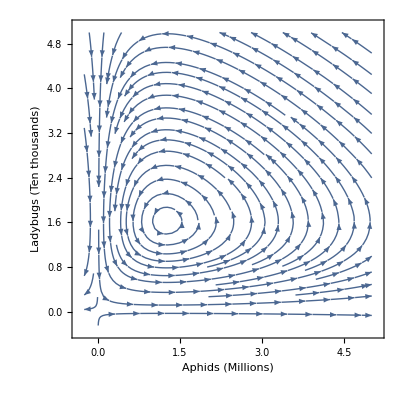

```mathematica
basicplot = StreamPlot[{r*A-α*A*L,-c*L+β*A*L},{A,-0.25,5},{L,-0.25,5},Axes->True,AxesLabel->{"A","L"},Frame->True,FrameLabel->{"Aphids (Millions)","Ladybugs (Ten thousands)"},ImageSize->Full]
```

We can also visualize the nullcline plot to get a better image of the equilibria.

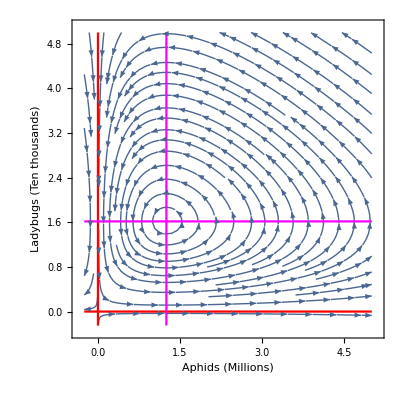

```mathematica
Show[basicplot,
ContourPlot[{A==0,L==0,A==0.1/0.08,L==0.21/0.13},{A,-0.25,5},{L,-0.25,5},ContourStyle->{Red,Red,Magenta,Magenta},ContourLabels->True],LabelStyle->{Black,30},ImageSize->Full,ContourLabels->True]
```

Pesticides effect:

```mathematica
Manipulate[StreamPlot[{r*A-α*A*L-f*A,-c*L+β*A*L-f*L},{A,-0.25,5},{L,-0.25,5},Axes->True,Frame->True,AxesLabel->{"A","L"},FrameLabel->{"Aphids (Millions)","Ladybugs (Ten thousands)"}],{f,0,0.1}]
```